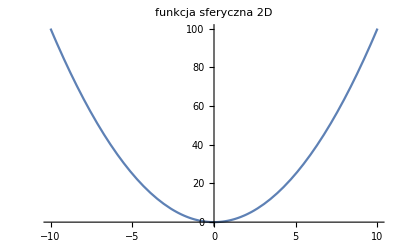

-Graphics3D-

```mathematica
(*Dawid Bitner*)
(*Zadanie 1-prezentacja wynków*)
(*zad1*)
(*funkcja sferyczna*)
SphereFunction2D[x_]=x^2;
SphereFunction3D[x_,y_]=x^2+y^2;
Plot[SphereFunction2D[x],{x,-10,10}, PlotLabel->"funkcja sferyczna 2D"]
Plot3D[SphereFunction3D[x,y],{x,-10,10},{y,-10,10}, PlotLabel->"funkcja sferyczna 3D"]
```

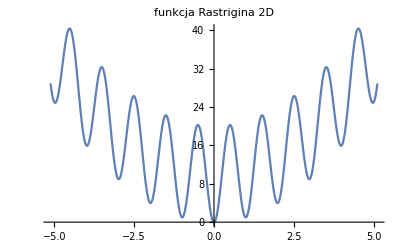

-Graphics3D-

```mathematica
(*funkcja Rastrigina*)
RastringerFunction2D[x_]=10+(x^2-10*Cos[2*Pi*x]);
RastringerFunction3D[x_,y_]=10+((x^2-10*Cos[2*Pi*x])+(y^2-10*Cos[2*Pi*y]));
Plot[RastringerFunction2D[x],{x,-5.12,5.12},PlotLabel->"funkcja Rastrigina 2D"]
Plot3D[RastringerFunction3D[x,y],{x,-5.12,5.12},{y,-5.12,5.12}, PlotLabel->"funkcja Rastrigina 3D"]
```

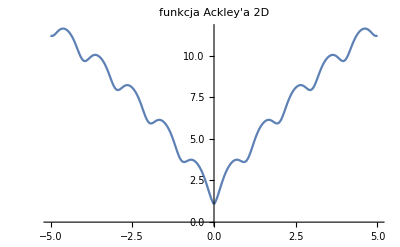

-Graphics3D-

```mathematica
(*funkcja Ackley'a*)
AckleyFunction2D[x_]=-20 Exp[-0.2*Sqrt[0.5*x^2]]-Exp[0.5*Cos[2*Pi*x]]+E+20;
AckleyFunction3D[x_,y_]=-20 Exp[-0.2*Sqrt[0.5*(x^2+y^2)]]-Exp[0.5*(Cos[2*Pi*x]+Cos[2*Pi*y])]+E+20;
Plot[AckleyFunction2D[x],{x,-5,5},PlotLabel->"funkcja Ackley'a 2D"]
Plot3D[AckleyFunction3D[x,y],{x,-5,5},{y,-5,5},PlotLabel->"funkcja Ackley'a 3D"]
```

```mathematica
(* dolina Rosenbrocka *)
```

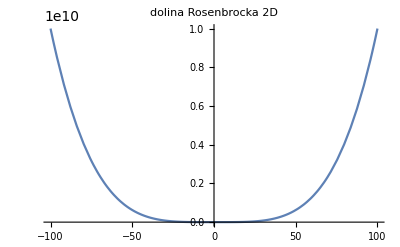

-Graphics3D-

```mathematica
RosenbrockFunction2D[x_]=100*(-x^2)^2+(1-x)^2;
RosenbrockFunction3D[x_,y_]=100*(y-x^2)^2+(1-x)^2;
Plot[RosenbrockFunction2D[x],{x,-100,100}, PlotLabel-> "dolina Rosenbrocka 2D"]
Plot3D[RosenbrockFunction3D[x,y],{x,-10,10},{y,-100,100}, PlotLabel-> "dolina Rosenbrocka 3D"]
```

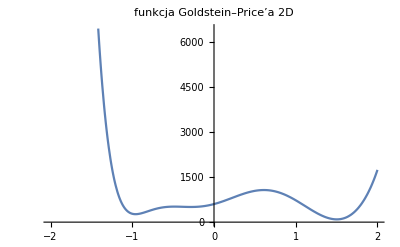

-Graphics3D-

```mathematica
(* funkcja Goldstein–Price’a *)
GoldsteinPriceFunction2D[x_]=(1+(x+1)^2*(19-14x+3x^2))*(30+(2x)^2*(18-32x+12x^2));
GoldsteinPriceFunction3D[x_,y_]=(1+(x+y+1)^2*(19-14x+3x^2-14y+6x*y+3y^2))*(30+(2x-3y)^2*(18-32x+12x^2+48y-36x*y+27y^2));
Plot[GoldsteinPriceFunction2D[x],{x,-2,2}, PlotLabel-> "funkcja Goldstein–Price’a 2D"]
Plot3D[GoldsteinPriceFunction3D[x,y],{x,-2,2},{y,-2,2}, PlotLabel-> "funkcja Goldstein–Price’a 3D"]
```

```mathematica
(* funkcja Hölder table *)
HolderTableFunction3D[x_,y_]=-Abs[Sin[x]*Cos[y]*Exp[Abs[1- (Sqrt[x^2+y^2])/Pi]]];
Plot3D[HolderTableFunction3D[x,y],{x,-10,10},{y,-10,10}, PlotLabel->"funkcja Hölder table 3D"]
```

-Graphics3D-

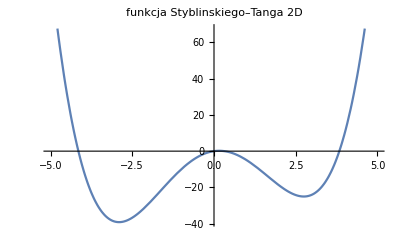

-Graphics3D-

```mathematica
(* funkcja Styblinskiego–Tanga *)
StyblinskiTangFunction2D[x_]=(x^4-16x^2+5x)/2;
StyblinskiTangFunction3D[x_,y_]=((x^4+y^4)-16*(x^2+y^2)+5*(x+y))/2;
Plot[StyblinskiTangFunction2D[x], {x,-5,5},PlotLabel->"funkcja Styblinskiego–Tanga 2D"]
Plot3D[StyblinskiTangFunction3D[x,y],{x,-5,5},{y,-5,5}, PlotLabel-> "funkcja Styblinskiego–Tanga 3D"]
```

```mathematica
(*zad2*)
PML[it_,numberOfPoints_,f_,down_,upper_]:=Module[{x,y,points,bests={},values={},bestScores={},averages={}},For[i=1,i≤it,i++,
points={};
values={};
For[j=1,j≤numberOfPoints,j++,x=RandomReal[{down[[1]],upper[[1]]}];
y=RandomReal[{down[[2]],upper[[2]]}];
points=Append[points,{x,y}];
values=Append[values,f[x,y]];];
minimum=Min[values];
pos=Position[values,minimum];
best=points[[pos[[1]]]];
avg=Mean[values];
bests=Append[bests,{minimum,best[[1,1]],best[[1,2]]}];
bestScores=Append[bestScores,minimum];
averages=Append[averages,avg];];
bestPos=Position[bests,Min[bestScores]];
Print["Najlepszy: ",bests[[bestPos[[1,1]],1]]," w punkcie: ",bests[[bestPos[[1,1]],2]],",",bests[[bestPos[[1,1]],3]]];
Print[ListLinePlot[bestScores, PlotLabel->"Najlepsze"] ];
Print[ListLinePlot[averages, PlotLabel->"Średnie"]];
Print[bestScores];
Print[averages];

];
```

Najlepszy: -19.1748 w punkcie: 8.10731,-9.6384

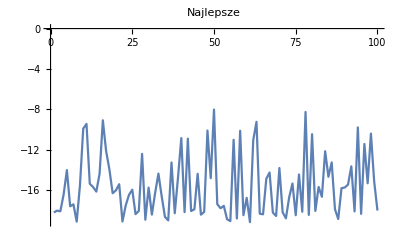

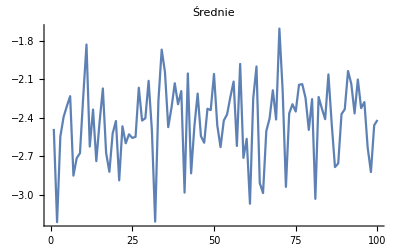

{-18.2134,-18.0375,-18.0991,-16.4473,-14.022,-17.6018,-17.4112,-19.1272,-15.5283,-9.91195,-9.44,-15.3684,-15.6966,-16.1523,-14.3857,-9.08646,-12.1389,-13.9371,-16.3131,-16.0277,-15.4176,-19.1118,-17.5104,-16.472,-15.9647,-18.3796,-18.068,-12.4102,-18.934,-15.7521,-18.4275,-16.2701,-14.3676,-16.6167,-18.6551,-19.0054,-13.2638,-18.2924,-14.7165,-10.8508,-18.1843,-10.9058,-18.0764,-17.9004,-14.3863,-18.4343,-18.1638,-10.0991,-14.8187,-8.02527,-17.395,-17.7965,-17.5619,-18.8925,-19.0745,-11.0197,-18.814,-10.1223,-18.4886,-16.7686,-19.1748,-11.0437,-9.23661,-18.3384,-18.4011,-14.8772,-14.2592,-18.228,-18.5677,-13.8111,-18.2053,-18.7957,-16.7038,-15.3473,-18.4909,-14.4539,-18.1481,-8.26346,-18.4585,-10.4632,-18.066,-15.6859,-16.6632,-12.149,-14.6827,-13.2547,-17.892,-18.8655,-15.8068,-15.7448,-15.4598,-13.6464,-18.1123,-9.7874,-18.3552,-11.433,-15.3237,-10.4058,-15.1637,-18.0278}

{-2.48582,-3.21258,-2.54533,-2.39217,-2.30826,-2.23117,-2.85007,-2.71391,-2.67536,-2.23507,-1.82864,-2.62359,-2.33521,-2.7374,-2.43312,-2.17074,-2.67383,-2.8204,-2.52191,-2.42441,-2.88714,-2.46571,-2.59813,-2.52821,-2.55628,-2.54835,-2.16508,-2.42107,-2.40291,-2.11114,-2.49701,-3.20875,-2.26617,-1.86803,-2.04338,-2.47238,-2.32131,-2.13021,-2.2938,-2.19129,-2.98242,-2.05418,-2.83249,-2.46513,-2.21061,-2.54232,-2.59386,-2.32939,-2.33887,-2.05778,-2.45843,-2.62824,-2.42054,-2.37326,-2.2379,-2.11731,-2.61921,-1.97967,-2.71192,-2.5631,-3.06925,-2.24639,-1.99955,-2.90785,-2.9861,-2.50252,-2.40499,-2.18494,-2.41294,-1.7043,-2.18729,-2.93781,-2.36591,-2.29371,-2.35104,-2.14229,-2.13734,-2.2453,-2.49386,-2.25394,-3.03119,-2.2372,-2.32767,-2.41007,-2.06143,-2.44402,-2.78367,-2.75509,-2.37123,-2.33267,-2.03488,-2.13538,-2.36549,-2.10124,-2.32431,-2.27698,-2.63011,-2.82248,-2.45768,-2.41667}

```mathematica
(*zad3*)
PML[100,100,HolderTableFunction3D, {-10,-10}, {10,10}];
```

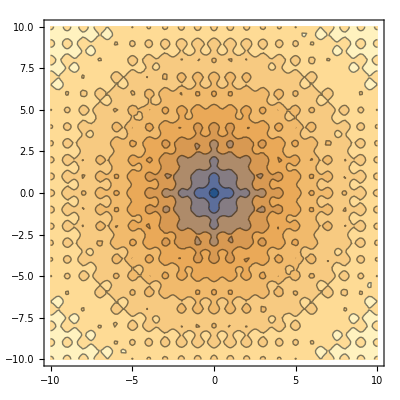

```mathematica
ContourPlot[AckleyFunction3D[x,y],{x,-10,10},{y,-10,10}]
```